```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

```mathematica
(* Write Module to Count number of roots in a function *)
(* From https://www.physicsforums.com/threads/find-all-roots-of-an-interpolating-function-in-mathematica.612362/ *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
Print[zeros];
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
If[First[zeros]==xmin,If[ifun[xmin]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
f[x_]:=x^4-x^2
countZeros[f,-2,2,0.1]
```

{-1.,-1.01172×10^-8,1.}

3

```mathematica
countAllZeros[ifun_,xmin_,xmax_,dx_,hardLim_]:=Module[{z,ztot,num,ii},
z=countZeros[ifun,xmin,xmax,dx];
Print["number of zeros for the function is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[x_]=D[ifun[x],{x,ii}];
If[f[x_]==0,Break[]];
z=countZeros[f,xmin,xmax,dx];
Print["number of zeros for ",ii,"th derivative is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
f[x_]:=x^4-x^2
countAllZeros[f,-10,10,0.1,1]
```

```mathematica
findZϵ[ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ϵsr,f,z,num,ii,ztot},
ϵsr[x_]:=1/2*(vp[x]/v[x])^2;
f[n_]:=ϵsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZη[ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ηsr,f,z,num,ii,ztot},
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]];
f[n_]:=ηsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ηsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ηsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ηsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of η is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findH[v_]:=Module[{h,hsq},
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
Return[{h,hsq}]]
```

```mathematica
findICsr[v_,vp_,ni_,prints_]:=Module[{ϕ0list,ϕ0index,ϕ0,f,ϕi1,ϕpi1},
ϕ0list = NSolve[vp[x]==√2*v[x],x];
ϕ0list = Union[ϕ0list,NSolve[vp[x]==-√2*v[x],x]];
Print["ϕ0list = ",ϕ0list];
ϕ0index = Input["Enter the index for the ϕ0 you want to use: \n(Counting starts at 1)"];
ϕ0 = x/.ϕ0list[[ϕ0index]];
If[prints,Print["ϕ0 = ",ϕ0]];
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
(* If[prints,Print["f[t] = ",f[t]]]; *)
(*ϕi1= t/.Last[NSolve[ni==f[t],t]];*)
ϕi1= t/.Last[FindRoot[ni-f[t],{t,20}]];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
Return[{ϕi1,ϕpi1}]]
```

```mathematica
findICshifted[v_,ϕsol1_,prints_,plots_]:=Module[{ϵ1,n1,ϕi2,ϕpi2},
(* Find ϵ1 *)
ϵ1=findϵ[v,ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
(* Find the new initial conditions *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
Return[{ϕi2,ϕpi2}]]
```

```mathematica
solveKG[hsq_,vp_,ni_,nf_,ϕi1_,ϕpi1_,plots_]:=Module[{ϕsol1},
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol1"},GridLines->{{-1,-1.2},{1}}]]];
Return[ϕsol1]]
```

```mathematica
findϵ[v_,ϕsol_]:=Module[{ϕp,hsq,ϵ},
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
(* took out a Re[] just inside the Evaluate[] *)
Return[ϵ]]
```

```mathematica
findϕsol[v_,vp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_]:=Module[{h,hsq,ϕi1,ϕpi1,ϕsol1,ϕi2,ϕpi2,ϕsol2},
(* Define the hubble parameter *)
{h,hsq}=findH[v];
(* Find the slow roll initial conditions *)
{ϕi1,ϕpi1}=findICsr[v,vp,ni,prints];
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = solveKG[hsq,vp,ni,nf,ϕi1,ϕpi1,plots];
(* Find the new initial conditions and re-solve the KG equation *)
{ϕi2,ϕpi2}=findICshifted[v,ϕsol1,prints,plots];
ϕsol2 = solveKG[hsq,vp,ni2,nf2,ϕi2,ϕpi2,plots];
(* Note: before I had it integrating from nf2 to ni2 *)
If[prints,Print["ϕsol2[60] = ",ϕ[60]/.ϕsol2]];
Return[ϕsol2]]
```

```mathematica
findNsR[v_,vp_,ϕsol2_,ni2_,nf2_,plots_,prints_] := Module[{ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Find ϵ2 *)
ϵ2 = findϵ[v,ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,nf2,ni2},AxesLabel->{N,"ns"}]]];
Return[{ns[n],r[n],ϵ2}]];
```

```mathematica
findSRparams[v_,vp_,vpp_,ϕsol2_,ni2_,nf2_,prints_,plots_]:=Module[{ϵsr,ϵsrL,ηsr,ηsrL},
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[1/2*(vp[x]/v[x])^2],{x,0,30},AxesLabel->{"ϕ","ϵ[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
Return[{ϵsr,ηsr}]]
```

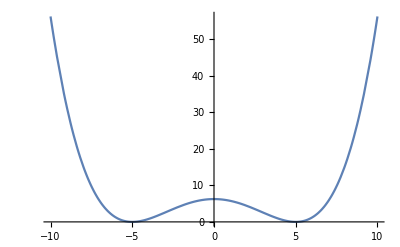

```mathematica
(* Define an inflationary potential *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(0.03)*x^4; *)
v[x_]:=(0.01)*(x^2-(5)^2)^2;
Plot[v[x],{x,-10,10}]
(* v[x_] := 1-1/2*(0.7)^2*x^2+(44^2/0.7)*x^4; *)
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -1.2; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
```

ϕ0list = {{x→-6.61037},{x→-5.},{x→-5.},{x→-3.78194},{x→3.78194},{x→5.},{x→6.61037}}

ϕ0 = 3.78194

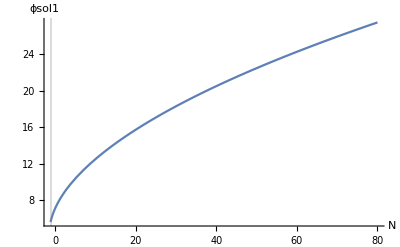

At n = 0, ϵ1 = 0.471482

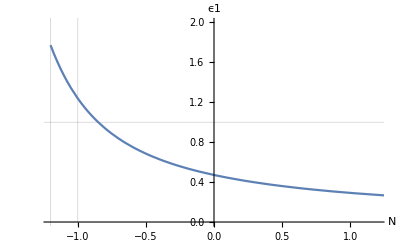

At n1 = -0.849809, ϵ1 = 1.

ϕi2 = 27.32

ϕpi2 = 0.151212

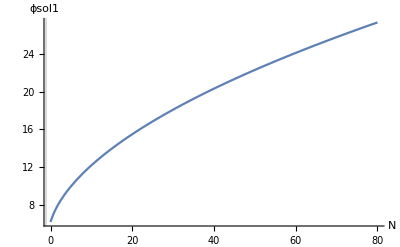

ϕsol2[60] = 24.0927

At n = 0, ϵ1 = 1.

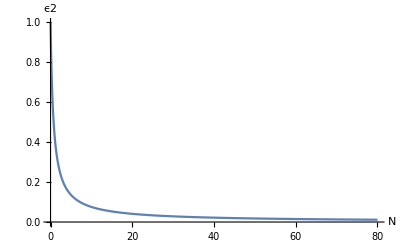

ns[60] = 0.954481

r[60] = 0.239561

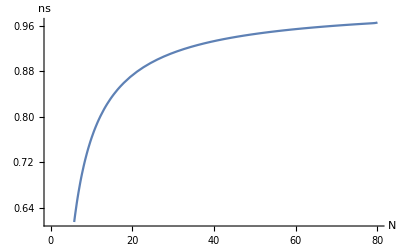

ϵsr[0] = 1.75359

ϵsr[60] = 0.0150508

ϵsrL[0] = 1.32423

ϵsrL[60] = 0.0150116

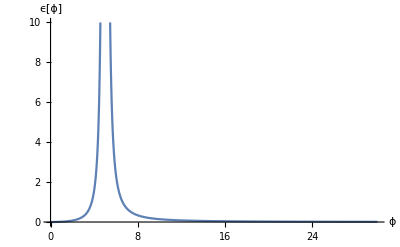

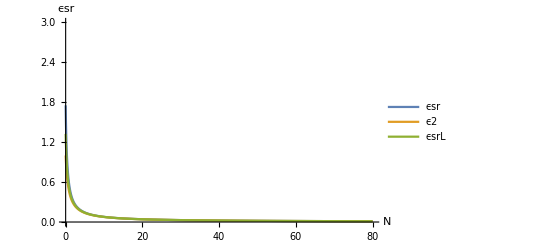

ηsr[0] = 2.05659

ηsr[60] = 0.0222521

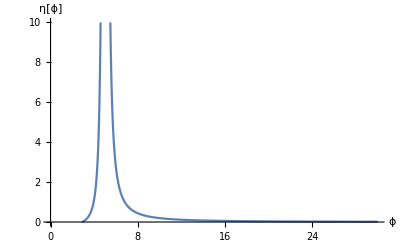

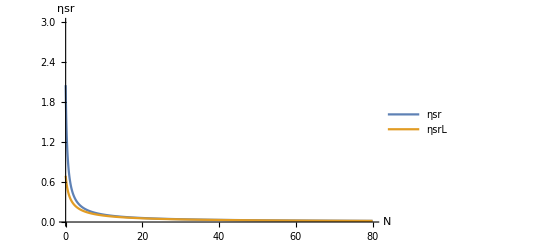

ns[60] = 0.954481 and r[60] = 0.239561

ns[50] = 0.945936 and r[50] = 0.283911

```mathematica
ϕsol2=findϕsol[v,vp,ni,nf,ni2,nf2,n1guess,True,True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True]; 
{ϵsr,ηsr} = findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True];
(* Plots,Prints *)
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

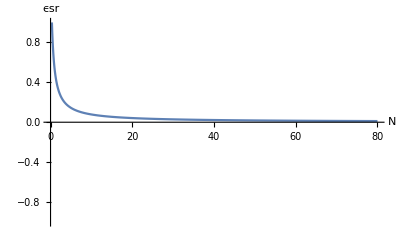

FindRoot::reged: The point {80.} is at the edge of the search region {0., 80.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

{80.}

number of zeros for ϵsr is 0

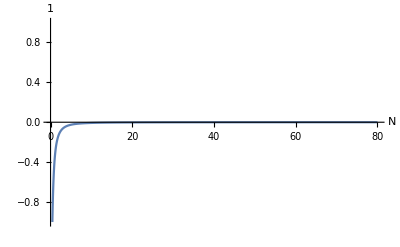

{80.}

number of zeros for 1th derivative of ϵ is 0

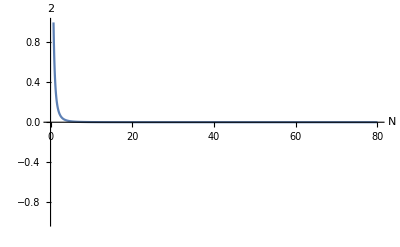

{80.}

number of zeros for 2th derivative of ϵ is 0

FindRoot::reged: The point {80.} is at the edge of the search region {0., 80.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

{80.}

number of zeros for the function is 0

{80.}

number of zeros for 1th derivative is 0

{80.}

number of zeros for 2th derivative is 0

```mathematica
Zϵ = findZϵ[ϕsol2,nf2,ni2,0.1,5];
If[prints,Print["Zϵ = ",
Zϵ]];
Zη = countAllZeros[ηsr,nf2,ni2,0.1,5];
If[prints,Print["Zη = ",
Zη]];
```

```mathematica
Zϵ = findZϵ[ϕsol,nf2,ni2,0.1,5];
Print["Zϵ = ",Zϵ];
```

```mathematica
Zη = findZη[ϕsol,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
MaxValue[ϵsr[n],n]
Plot[Evaluate[ϵsr[n]],{n,0,80},AxesLabel->{N,"ϵsr"},PlotRange->{0,2}]
f1[n_]=D[ϵsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ϵsr1"},PlotRange->{-1,1}]
f2[n_]=D[ϵsr[n],{n,2}];
MaxValue[f2[n],n]
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ϵsr2"},PlotRange->{-1,1}]
```

```mathematica
Plot[Evaluate[ηsr[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f1[n_]=D[ηsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f2[n_]=D[ηsr[n],{n,2}];
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ηsr2"}]
```

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 80; nf = -1.2; ni2 = 80; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35
Do[
Clear[v,vp,ns,r];
v[ϕ_] := ϕ^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
{ns,r} = findNsR[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```